Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Temperature trend with last value of ntemp in the cycle, for n=15

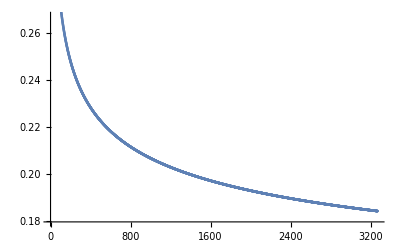

% of 2-opt vs ntemp (t0=0) (fixed n=15)

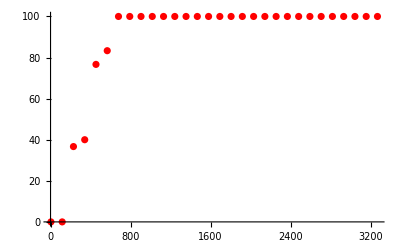

Polynomial fit % 2-opt (t0=0) (fixed n=15)

-31.0096+6.3203 y^0.5-0.0766046 y+1.42322×10^-6 y^2

% of 3-opt vs ntemp (t0=0) (fixed n=15)

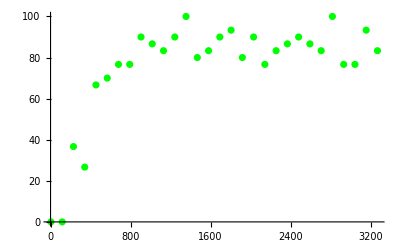

Polynomial fit % 3-opt (t0=0) (fixed n=15)

-24.5634+4.97233 y^0.5-0.0519393 y-9.1556×10^-7 y^2

% of 2-opt and 3-opt vs ntemp (t0=0) (fixed n=15)

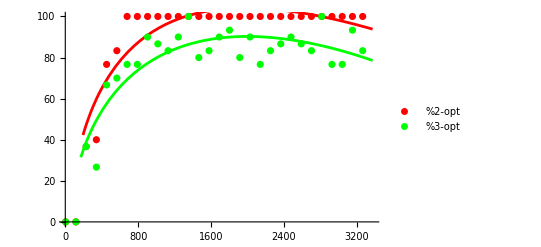

% of 2-opt vs ntemp (t0>0) (fixed n=15)

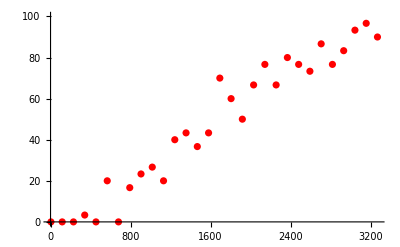

Polynomial fit % 2-opt (t0>0) ( fixed n=15)

6.32681-1.87287 y^0.5+0.0874999 y-8.62799×10^-6 y^2

% of 3-opt vs ntemp (t0>0) (fixed n=15)

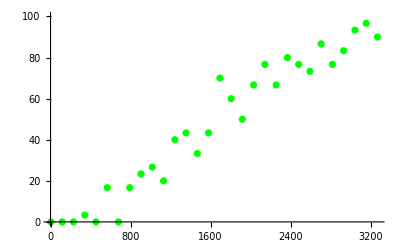

Polynomial fit % 3-opt (t0>0) (fixed n=15)

6.68285-1.94542 y^0.5+0.0891188 y-8.76112×10^-6 y^2

% of 2-opt and 3-opt vs ntemp (t0>0) (fixed n=15)

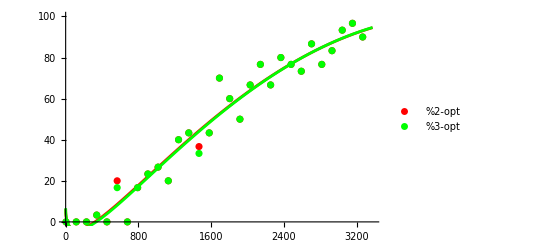

ntemp s.t. %2-opt=68% vs #cities (t0=0)

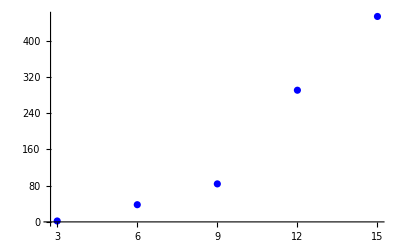

11.2456 z-2.62198 z^2+0.0400153 z^4-0.000100934 z^6

ntemp s.t. %2-opt=68% vs #cities (t0>0)

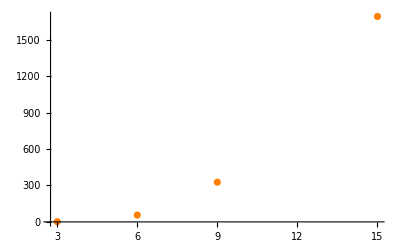

3.82949 z-1.77064 z^2+0.0812401 z^4-0.000182635 z^6

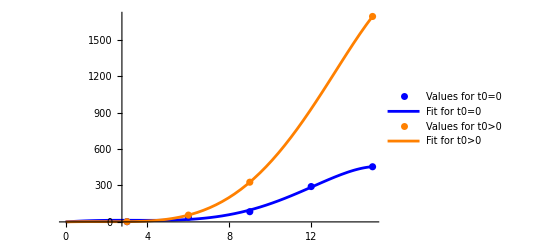

Minimum distances against ntemp for t0=0 and non, at n=15 and averaged over the replicas

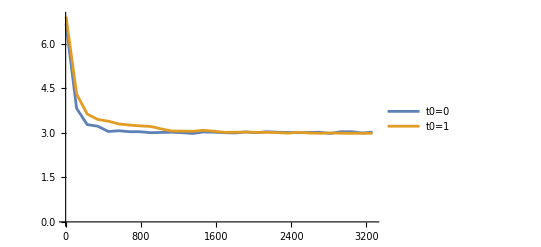

(%3-opt / %2-opt) vs ntemp for t0=0 and t0>0, (fixed n=15). Negative value are put in case of zero 2opt replicas:

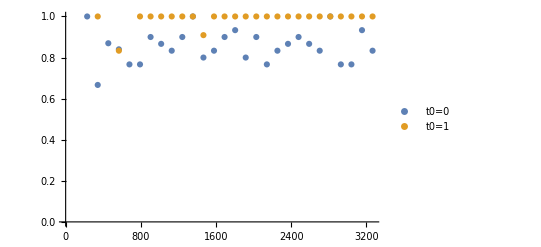

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

Table::iterb: Iterator {itemp,0,Round[Last[{}]]} does not have appropriate bounds.

Last::nolast: {} has zero length and no last element.

Table::iterb: Iterator {i,1,1+Round[Last[{}]]} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,1.+Round[Last[{}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
(* In this file we give an estimation of the computational cost for the annealing algorithm in terms of number of temperature steps needed to reach some goodness in the solutions. The goodness criterion is based on the percentage of 2(3)_optimal solutions among all replica solutions. We calculate for different values of the number n of cities the temperature steps needed to reach 68% of 2(3)_optimal solutions and we plot those costs as a funcion of n. We find the expected nonlinear behavior. We also plot the minimum distances averaged over all replica varying the maximum number of temperature steps. All these plots and analysis are done for the case of t0=0 and t0≠0. The possible "move strategy" can be chosen among TwoMoves and ThreeMoves *)


Clear[z]
Clear[y]



(* PARAMETERS *)

flagg=0;   (* 0 -> fixed ntempmax=n^3 (good for DMIN vs cost and %3-opt/%2-opt vs cost plots because both t0=0 case and t0=1 case share the same domain), 1 -> variable ntempmax (good for %2(3)opt vs cost and opt_cost vs n plots because the interval is centered around opt_cost and less itarations are performed) *)

(* setting the city configuration *)
nmin=3; (* min num of cities in For loop *)
nmax=15; (* max num of cities in For loop *)
nincr=3; (* increment in For loop *)
nplot=15; (* fixed num of cities for which some analysis will be carried out (perc, DMIN); make sure it's covered by the sequence nmin+ C*nincr *)
citiesConfiguration=1; (* 1 -> random points; 2 -> regular polygon *)

(* setting move strategy *)
moveStrategy=2; (* 2 -> Lin's 2 step move (TwoMoves) ; 3 -> Lin's 3 step move (ThreeMoves) *) 

(* setting the cooling strategy *)
annealingStrategy=4; (* 1 -> t=t0-k*itemp ; 2 -> t=t0/itemp ; 3 -> t=t0^(1/itemp)-1 ; 4 -> t=t0/Log[E+k*itemp] *)
t0nz=1; (* algorithm will be run for t0=0 and t0=t0nz : some Non-Zero value *)
k =1000000*E;     (* linear/logaritmic temperature vatiation *)
nsteps=1;     (* num of steps at fixed temperature *) 

nrepl=30; (* num of replicas with different initial state: the results will be averaged over replicas to have statistical significance *)



(* FUNCTIONS *)

(* function to calculate the total distance of a route adding the distance of each link there present. It is based on the definition of a distance matrix (see below) *)
distcalc[seq_]:=Module[{d=0,i=1},
For[i=1,i<=n,i++,
indeces=seq[[i;;i+1]];
d=d+dist[[indeces[[1]],indeces[[2]]]];
];
d
];

(* function to implement the "TwoMoves" move where two random cities of the sequence are exchanged and the sub-sequence contained by them is inverted *)
TwoMoves[seq_]:= Module[{seqnew=Table[0,{i,n+1}]},
seqnew=seq;
indeces=RandomInteger[{2,n},2];
indeces=Sort[indeces];
seqnew[[indeces[[1]];;indeces[[2]]]]=Reverse[seq[[indeces[[1]];;indeces[[2]]]]];
seqnew
];

(* function to implement the "ThreeMoves", for description of this move steps see image in the slides *)
ThreeMoves[seq_]:= Module[{seqnew=Table[0,{i,n+1}]},
seqnew=seq;
indeces=RandomInteger[{1,n},3];
While[indeces[[1]]==indeces[[2]] || indeces[[1]]==indeces[[3]] || indeces[[2]]==indeces[[3]],
indeces=RandomInteger[{1,n},3];
];
indeces=Sort[indeces];
x=RandomReal[];
If[x<0.5,
seqnew[[indeces[[1]]+1;;indeces[[1]]+indeces[[3]]-indeces[[2]]]]=seq[[indeces[[2]]+1;;indeces[[3]]]];
seqnew[[indeces[[1]]+indeces[[3]]-indeces[[2]]+1;;indeces[[3]]]]=seq[[indeces[[1]]+1;;indeces[[2]]]],
seqnew[[indeces[[1]]+1;;indeces[[1]]+indeces[[3]]-indeces[[2]]]]=Reverse[seq[[indeces[[2]]+1;;indeces[[3]]]]];
seqnew[[indeces[[1]]+indeces[[3]]-indeces[[2]]+1;;indeces[[3]]]]=seq[[indeces[[1]]+1;;indeces[[2]]]];
];
seqnew
];



nV={};
nV0={};
optcost={};
optcost0={};
cost={};
cost0={};
perc2={};
perc20={};
perc3={};
perc30={};
DMIN1={};
DMIN0={};

(* ITERATIONS ON DIFFERENT NUMBER OF CITIES *)
For[n=nmin,n<=nmax,n=n+nincr,

(* MATRIX OF DISTANCES *)
Switch[citiesConfiguration,
1,coords=RandomReal[1,{n,2}] , (* create a set of coordinates for n cities in a 1x1 space centered in (0.5,0.5) *)
2,coords=Table[{Cos[2Pi i/n],Sin[2Pi i /n]},{i,n}]; (* coordinates of a polygonal city configuration *)
];
MatrixForm[coords];
dist=Table[0,{i,n},{j,n}];    (* initialize/clear the distance matrix *)
For[i=1,i<=n,i++,
For[j=1,j<=i,j++, 
dist[[i,j]]=Norm[coords[[i]]-coords[[j]]];
];
];
dist=dist+Transpose[dist]; 
MatrixForm[dist];

(* ITERATION ON TWO DIFFERENT VALUES OF t0, = 0 AND > 0 *) 
For[t0=0,t0<=t0nz, t0=t0+t0nz, (* one possible value of t0>0 (t0nz:t0nonzero) only *)

(* ITERATION ON DIFFERENT NUMBER OF MAX TEMPERATURE STEPS (COST) *)
flag=1; (* needed to enter the If condition for the tunable ntempmax only once *)
ntempmax=n^3; (* maximum (possible) value of ntemp, if it isn't modified while running the cycle on ntemp stops for the value set here *)
For[ ntemp=Round[Sqrt[n]],ntemp<=ntempmax,ntemp=ntemp+0.5*n^2,(* ntemp=0.005*n^3,ntemp<=1.125*n^3,ntemp=ntemp+0.08*n^3, *)  (* Here an "a posteriori" range for ntemp is set in order to always be sure that the optimal cost, for which %2-opt >= 68% (but it can be changed), is at the center. The interval is however sampled uniformly *)

(* SIMULATED ANNEALING SOLUTIONS WITH FIXED NUMBER OF TEMPERATURE STEPS *)
SEQMIN=Table[0,{i,nrepl},{j,n+1}];
DMIN=Table[0,{i,nrepl}];
For[irepl=1,irepl<=nrepl,irepl++, 
rndmsmpl=RandomSample[Range[n]]; (* different starting routes at each replica *)
seq0=Join[rndmsmpl,{rndmsmpl[[1]]}]; (* to have a closed loop *)
d0=distcalc[seq0];
seqmin=seq0;
dmin=d0;
For[itemp=0,itemp<=ntemp,itemp++,
Switch[annealingStrategy,
1,t=t0-k*itemp,
2,t=t0/itemp,
3,t=t0^(1/itemp)-1,
4,t=t0/Log[E+k*itemp];
];
For [isteps=1,isteps<=nsteps,isteps++,
Switch[moveStrategy,
2,seq1=TwoMoves[seq0],
3,seq1=ThreeMoves[seq0];
];
d1=distcalc[seq1];
If[d1<d0,
seq0=seq1;
d0=d1;
If[d0<dmin,
seqmin=seq0;
dmin=d0;
],
prob=Exp[-(d1-d0)/t];
r=RandomReal[];
If[r<prob,
seq0=seq1;
d0=d1;
];
];
];
];
SEQMIN[[irepl]]=seqmin;
DMIN[[irepl]]=dmin;
];

(* 2(3)-OPTIMAL SOLUTIONS SEARCH: this block is meant to calculate how many of the solutions in DMIN are 2(3)-optimal. 2(3)-optimality means that the solution is a minimum for any change of any 2(3) links in the sequence *)
iopt=0;
SEQOPT2={};
DOPT2={};
For[irepl=1,irepl<=nrepl,irepl++,
check=1;
For[i=2,i<=n-1,i++,
For[j=i+1,j<=n,j++,
neighbor=SEQMIN[[irepl]];
neighbor[[i;;j]]=Reverse[SEQMIN[[irepl]][[i;;j]]];
If[distcalc[neighbor]<DMIN[[irepl]],
check=0;
];
];
];
If[check==1,
SEQOPT2=Join[SEQOPT2,{SEQMIN[[irepl]]}];
DOPT2=Join[DOPT2,{DMIN[[irepl]]}];
iopt++;
];
];
n2opt=iopt;

iopt=0;
SEQOPT3={};
DOPT3={};
For[iopt2=1,iopt2<=Length[SEQOPT2],iopt2++, (* we look for 3-opt in the subset of 2-opt because we know that the set of (lambda+1)-opt is contained in the set of lambda-opt *)
check=1;
For[i=1,i<=n-2,i++,
For[j=i+1,j<=n-1,j++,
For[k=j+1,k<=n,k++,
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=SEQOPT2[[iopt2]][[j+1;;k]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
neighbor=SEQOPT2[[iopt2]];
neighbor[[i+1;;i+k-j]]=Reverse[SEQOPT2[[iopt2]][[j+1;;k]]];
neighbor[[i+k-j+1;;k]]=SEQOPT2[[iopt2]][[i+1;;j]];
If[distcalc[neighbor]<DOPT2[[iopt2]],
check=0;
];
];
];
];
If[check==1,
SEQOPT3=Join[SEQOPT3,{SEQOPT2[[iopt2]]}];
DOPT3=Join[DOPT3,{DOPT2[[iopt2]]}];
iopt++;
];
];
n3opt=iopt;

(* CALCULATION OF % OF 2 AND 3 OPTIMAL SOLUTIONS IN ALL REPLICAS (perc2/3) FOR DIFFERENT VALUES OF ntemp AND FOR FIXED n=nplot; CREATION OF A VECTOR DMIN CONTAINING THE MEAN MINIMUM DISTANCE (AVERAGED OVER THE REPLICAS) FOR DIFFERENT VALUES OF ntemp AND FOR FIXED n=nplot; 0 differentiates the values obtained when t0=0 *)
If[n==nplot,
If[t0==0,
perc20=Join[perc20,{N[(n2opt*100)/nrepl]}]; 
perc30=Join[perc30,{N[(n3opt*100)/nrepl]}]; 
cost0=Join[cost0,{ntemp}];
DMIN0=Join[DMIN0,{Mean[DMIN]}];
ntempmax0=ntempmax,
perc2=Join[perc2,{N[(n2opt*100)/nrepl]}]; 
perc3=Join[perc3,{N[(n3opt*100)/nrepl]}]; 
cost=Join[cost,{ntemp}];
DMIN1=Join[DMIN1,{Mean[DMIN]}];
];
];

(* This block saves into a vector the "optimal cost", the cost (value of ntemp) that is needed to reach 68% of 2-optimal solution among all replicas solutions. The aim is to plot this optimal cost as a function of the num of cities n *)
If[((n2opt*100)/nrepl)>=68 && flag==1, 
If[t0==0,    
optcost0=Join[optcost0,{ntemp}];
nV0=Join[nV0,{n}],
optcost=Join[optcost,{ntemp}];
nV=Join[nV,{n}];
];
If[flagg==1,
ntempmax=ntemp*1.5; (* this command allows us to plot the percentages over an ntemp interval centered in ntemp s.t. 50% of 2-opt is obtained *)
];
flag=0;
];

];
];
];



(* PLOTS *)
 
(* PLOT OF TEMPERATURE VALUE t OVER itemp FOR LAST VALUE OF ntemp AND n=nplot *)
(*ListPlot[Transpose[{DMIN3movs,ntempV}]]*)
Print["Temperature trend with last value of ntemp in the cycle, for n=",nplot]
Switch[annealingStrategy,
1,tV=Table[t0-k*itemp,{itemp,0,Round[Last[cost]]}],
2,tV=Table[t0/itemp,{itemp,1,Round[Last[cost]]}],
3,tV=Table[t0^(1/itemp)-1,{itemp,1,Round[Last[cost]]}],
4,tV=Table[t0/Log[E+k*itemp],{itemp,0,Round[Last[cost]]}];
];
ListPlot[Transpose[{Table[i,{i,1,Round[Last[cost]]+1}],tV}]] (* +1 if strategy is with itemp starting from 0 *)


(* For the following plots it is useful to set flagg to 1 so to modify ntempmax and center the interval at 50%: this is done both to obtain a more aesthetic result and to limit ntemp in a reasonable way for every choice of n *)
(* PLOT OF 2(3)OPT% OVER COST AT t0=0 FOR n=nplot *) 
Clear[y];
Print["% of 2-opt vs ntemp (t0=0) (fixed n=",nplot,")"];
ListPlot[Transpose[{cost0,perc20}],PlotRange->{0,100},PlotStyle->Red] (* will do with n = nplot *)
Print["Polynomial fit % 2-opt (t0=0) (fixed n=",nplot,")"]
Clear[y];
polyfit20=Fit[Transpose[{cost0,perc20}],{1,y,y^0.5,y^2},y]
Print["% of 3-opt vs ntemp (t0=0) (fixed n=",nplot,")"];
ListPlot[Transpose[{cost0,perc30}],PlotRange->{0,100},PlotStyle->Green] (* will do with n = nplot *)
Print["Polynomial fit % 3-opt (t0=0) (fixed n=",nplot,")"]
Clear[y];
polyfit30=Fit[Transpose[{cost0,perc30}],{1,y,y^0.5,y^2},y]
Print["% of 2-opt and 3-opt vs ntemp (t0=0) (fixed n=",nplot,")"];
Show[ListPlot[Transpose[{cost0,perc20}],PlotStyle->Red,PlotLegends->{"%2-opt"}],Plot[polyfit20,{y,0,ntempmax0},PlotStyle->Red],ListPlot[Transpose[{cost0,perc30}],PlotStyle->Green,PlotLegends->{"%3-opt"}],Plot[polyfit30,{y,0,ntempmax0},PlotStyle->Green],PlotRange->{0,100}]

(* PLOT OF 2(3)OPT% OVER COST AT t0>0 FOR n=nplot *)
Print["% of 2-opt vs ntemp (t0>0) (fixed n=",nplot,")"];
ListPlot[Transpose[{cost,perc2}],PlotRange->{0,100},PlotStyle->Red] 
Print["Polynomial fit % 2-opt (t0>0) ( fixed n=",nplot,")"]
Clear[y];
polyfit2=Fit[Transpose[{cost,perc2}],{1,y,y^0.5,y^2},y]
Print["% of 3-opt vs ntemp (t0>0) (fixed n=",nplot,")"];
ListPlot[Transpose[{cost,perc3}],PlotRange->{0,100},PlotStyle->Green] 
Print["Polynomial fit % 3-opt (t0>0) (fixed n=",nplot,")"]
Clear[y];
polyfit3=Fit[Transpose[{cost,perc3}],{1,y,y^0.5,y^2},y]
Print["% of 2-opt and 3-opt vs ntemp (t0>0) (fixed n=",nplot,")"];
Show[ListPlot[Transpose[{cost,perc2}],PlotStyle->Red,PlotLegends->{"%2-opt"}],Plot[polyfit2,{y,0,ntempmax},PlotStyle->Red],ListPlot[Transpose[{cost,perc3}],PlotStyle->Green,PlotLegends->{"%3-opt"}],Plot[polyfit3,{y,0,ntempmax},PlotStyle->Green],PlotRange->{0,100}]

(* OPTIMAL COST vs NUMBER OF CITIES PLOT *)
Print["ntemp s.t. %2-opt=68% vs #cities (t0=0)"]
ListPlot[Transpose[{nV0,optcost0}],PlotRange->All,PlotStyle->Blue]
Clear[z];
polyfit0=Fit[Transpose[{nV0,optcost0}],{z,z^2,z^4,z^6},z]
Print["ntemp s.t. %2-opt=68% vs #cities (t0>0)"]
ListPlot[Transpose[{nV,optcost}],PlotRange->All,PlotStyle->Orange]
Clear[z];
polyfit=Fit[Transpose[{nV,optcost}],{z,z^2,z^4,z^6},z]
Show[ListPlot[Transpose[{nV0,optcost0}],PlotStyle->Blue,PlotLegends->{"Values for t0=0"}],Plot[polyfit0,{z,0,nmax},PlotStyle->Blue,PlotLegends->{"Fit for t0=0"}],ListPlot[Transpose[{nV,optcost}],PlotStyle->Orange,PlotLegends->{"Values for t0>0"}],Plot[polyfit,{z,0,nmax},PlotStyle->Orange,PlotLegends->{"Fit for t0>0"}],PlotRange->{{0,nmax},All}]


(* SET flagg = 0 so it doesn't modify ntempmax (which changes from t0=0 to t0≠0). When plotting parameters for t0=0 and non in the same figure they must have the same ntemp range! *)

(* PLOT OF DMIN FOR t0=0 AND t0=1 OVER ntemp, FOR n=nplot *)
Print["Minimum distances against ntemp for t0=0 and non, at n=",nplot," and averaged over the replicas"];ListLinePlot[{Transpose[{cost0,DMIN0}],Transpose[{cost,DMIN1}]},PlotLegends->{"t0=0","t0=1"},PlotRange->All]

(* PLOT OF RATIO BETWEEN 3-OPT% AND 2-OPT% OVER ntemp FOR t0=0 AND t0>0, n=nplot *)
Print["(%3-opt / %2-opt) vs ntemp for t0=0 and t0>0, (fixed n=",nplot,"). Negative value are put in case of zero 2opt replicas:"];
ratio=Table[0,{i,Length[perc2]}];
ratio0=Table[0,{i,Length[perc20]}];
For[i=1,i<=Length[perc2],i++,
If[perc2[[i]]==0,
ratio[[i]]=-0.2, (* just to avoid indeterminate values *)
ratio[[i]]=perc3[[i]]/perc2[[i]];
];
];
For[i=1,i<=Length[perc20],i++,
If[perc20[[i]]==0,
ratio0[[i]]=-0.2, (* just to avoid indeterminate values *)
ratio0[[i]]=perc30[[i]]/perc20[[i]];
];
];
ListPlot[{Transpose[{cost0,ratio0}],Transpose[{cost,ratio}]},PlotLegends->{"t0=0","t0=1"},PlotRange->{0,1}]
```